## Comparing the nuc & cyto intensity measurements of fix cell accumulation 15h experiments

### Importing files...

Import the csv file from Measure_cyto_nuc_bkg_AutoThreshold.ijm processed fix cell images, stained with Cy3-FLAG-Fab

```mathematica
myFileTL1=FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190226_*TL*/_Analysis/R*.csv"]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190226_fixed_TL_cy3_accum_15h/_Analysis/Results_msr_macro_TL1.csv}

```mathematica
myFileNT2=FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_NT_*/_Analysis/R*.csv" ]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190301_NT_fix_transf_cy3-flag-fab_accum/_Analysis/Results_msr_macro_NT.csv}

```mathematica
myFileTL2=FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_TL_*/_Analysis/R*.csv" ]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190301_TL_fix_transf_cy3-flag-fab_accum/_Analysis/Results_msr_macro_TL.csv}

```mathematica
myFileTA2=FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_TA_*/_Analysis/R*.csv" ]
```

{/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190301_TA_fix_transf_cy3-flag-fab_accum/_Analysis/Results_msr_macro_TA.csv}

```mathematica
myFileNames = Flatten@{myFileNT2, myFileTL1,myFileTL2,myFileTA2};
```

TEST :

```mathematica
(*testTLfile=FileNames["/Users/ccialek/Desktop/*.csv"]
```

```mathematica
(*myFileNames = testTLfile;
```

### Make Nuc/whole cell intensity graphs to visualize data...

```mathematica
mycsv = Import /@myFileNames;
mycsv[[1,1]]
Length@mycsv
(*CSV Files:   NT, TL1, TL2, TA*)
```

{,Area,Mean,Min,Max}

4

```mathematica
mymsrmts = Table[ Partition[ Flatten@mycsv[[i, 2;;All]] , 8(*4 bkgd, 2 nuc, 2 cyto*) *5 (*5 measureents, {"","Area","Mean","Min","Max"}*)]  ,{i,1,Length@mycsv,1}];
ncells = Length/@mymsrmts
```

{102,101,134,134}

```mathematica
myAreas = Table[ mymsrmts[[i,All,2;;All;;5]], {i,1,Length@mymsrmts}];
myMeans = Table[ mymsrmts[[i,All,3;;All;;5]],  {i,1,Length@mymsrmts}];
myMaxs = Table[ mymsrmts[[i,All,5;;All;;5]],  {i,1,Length@mymsrmts}];
```

```mathematica
ch1bkgs =  Table[ myMeans[[i,All,1;;2]], {i,1,Length@mymsrmts}];
meanCh1bkgs =  Table[ Min/@ch1bkgs[[i]] , {i,1,Length@mymsrmts}];
ch2bkgs =  Table[ myMeans[[i,All,3;;4]], {i,1,Length@mymsrmts}];
meanCh2bkgs =  Table[ Min/@ch2bkgs[[i]] , {i,1,Length@mymsrmts}];
```

Plots comparing the background at each corner...

Backgorund top corner vs background bottom corner

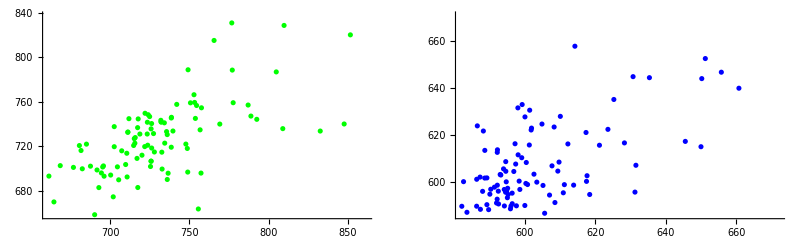
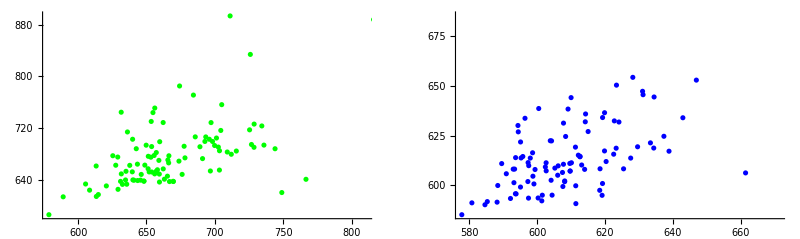
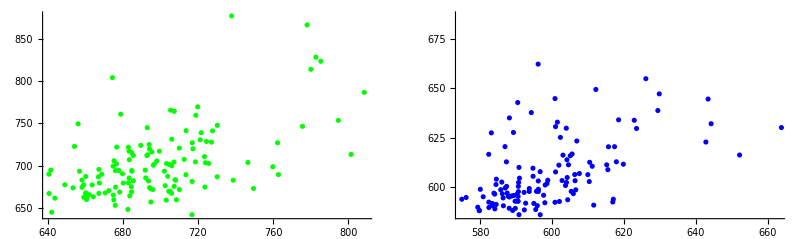
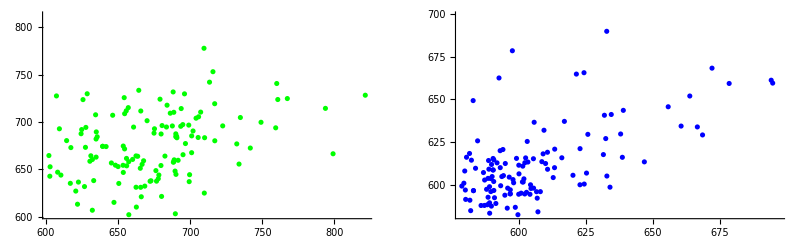

```mathematica
"Backgorund top corner vs background bottom corner"
Table[ GraphicsRow[{ ListPlot[ch1bkgs[[i]], PlotStyle->Green],
ListPlot[ch2bkgs[[i]], PlotStyle->Blue]   }], {i,1,Length@mymsrmts}]
```

```mathematica
ch1nuccyto= Table[ myMeans[[i, All,5;;6]] , {i,1,Length@mymsrmts}];
ch2nuccyto = Table[ myMeans[[i, All,7;;8]] , {i,1,Length@mymsrmts}];
```

Plots comparing the Nuc/Cyto ratios, to try to find out which measurement is better or more accurate:

{{102  cells measured,101  cells measured,134  cells measured,134  cells measured}}

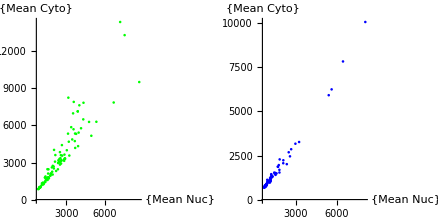
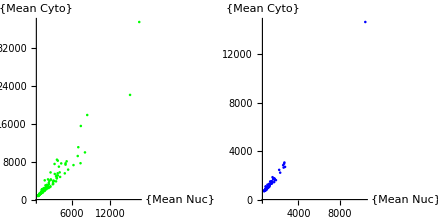
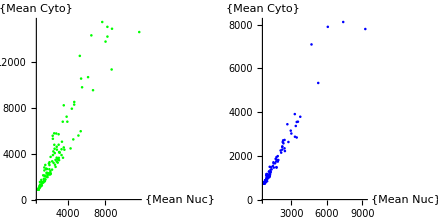
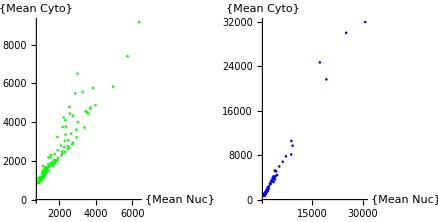

```mathematica
myPlotOptions = { AspectRatio-> 1, PlotRange->All, ImageSize-> 200, LabelStyle->{FontFamily->"Arial Narrow",14,GrayLevel[0]},   AxesLabel->{{"Mean Nuc"},{"Mean Cyto"}}}   ;

{ ncells  " cells measured"}

mynuccellgraphs = Table[ GraphicsRow[{   ListPlot[ch1nuccyto[[i]], PlotStyle->Green, myPlotOptions[[All]] ],
ListPlot[ch2nuccyto[[i]], PlotStyle->Blue, myPlotOptions[[All]] ]   
}] ,  {i,1,Length@mymsrmts}]
```

### BarWhisk plots of nuc intensity

#### Parameters...

```mathematica
myfont = BaseStyle->{FontFamily->"Arial Narrow",FontSize->22};
```

```mathematica
l=.4; m=.1; (*how wide your data is on your box/whisker plot*)
s=.0175; (*Size of plot markers*)
```

b =   ListPlot 
a =   data

### TEMP DEV! Remove bkgds...

```mathematica
Transpose /@ {myMaxs[[1]],myMeans[[1]] }  ;
```

```mathematica
myMaxs[[1]]//Length
```

102

```mathematica
a00 = ch1nuccyto[[All,All,2]] - meanCh1bkgs -100;
```

NOTE!!! You can use either 1 or 2. These two different measurements are either the NUC or NUC+CYTO. They should give ~same results....

#### Remove duplicates...

```mathematica
deleteDuplicateNucIntensities = DeleteDuplicates/@Sort/@Table[Table[SetPrecision[a00[[cell,ints]],3],{ints,1,Length@a00[[cell]]}],{cell,1,Length@a00}];
Length/@deleteDuplicateNucIntensities
DeleteDuplicates/@a00//Length/@#&
{" The # of removed duplicates =  " , (Length/@deleteDuplicateNucIntensities) - (DeleteDuplicates/@a00//Length/@#&)}
```

{96,99,126,130}

{101,100,134,133}

{ The # of removed duplicates =  ,{-5,-1,-8,-3}}

#### Log scale...

Use this line to use ALL cells, no deleted duplicates:

```mathematica
(* a = a00*)
```

Use this line to use non-duplicated cells:

```mathematica
a=deleteDuplicateNucIntensities;
```

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , ScalingFunctions->"Log2" ,PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ] ;
```

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,ScalingFunctions->"Log2" ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
```

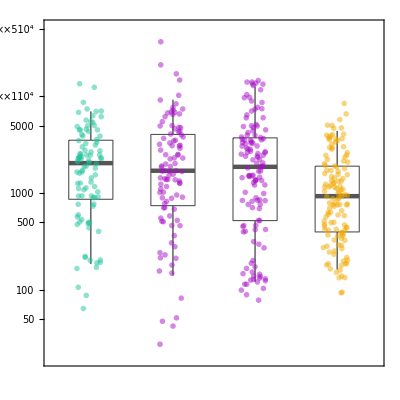

```mathematica
Show[   bwchart,b, AspectRatio -> 1,myfont]
```

#### Linear scale...

Use this line to use ALL cells, no deleted duplicates:

```mathematica
(* a = a00*)
```

Use this line to use non-duplicated cells:

```mathematica
a=deleteDuplicateNucIntensities;
```

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a[[n]] ] ], a[[n]] }], {n,1,Length@a}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ];
```

```mathematica
bwchart = BoxWhiskerChart[a,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,PlotRange-> {0,21000},  ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}];
```

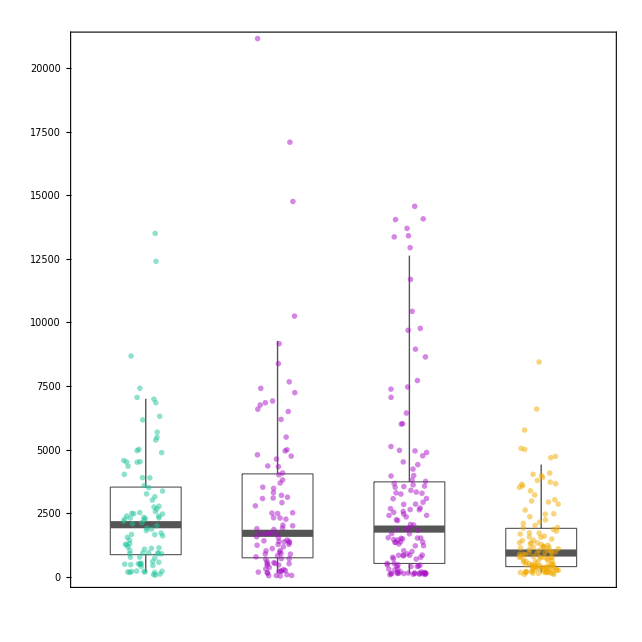

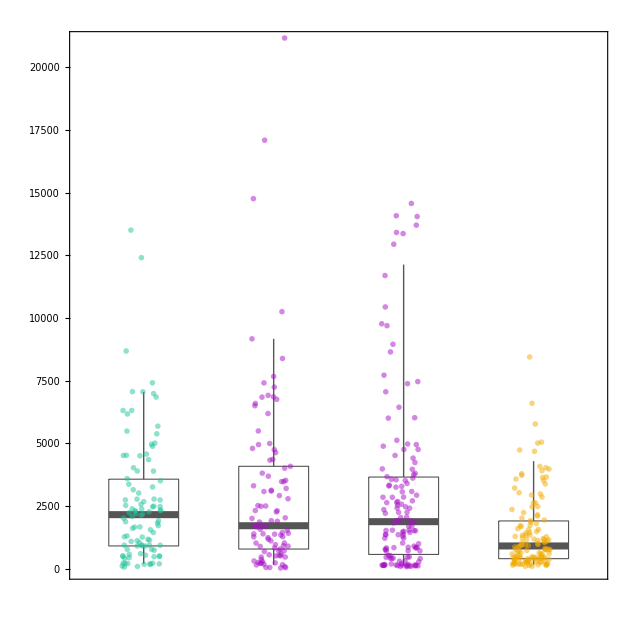

```mathematica
Show[   bwchart,b, AspectRatio -> 1,myfont]
```

#### ONLY Day2 data:

```mathematica
a0={a[[1]],a[[3]],a[[4]] };
```

```mathematica
b = ListPlot[Table[ Thread[{Table[RandomReal[ {n-l,n-m} ], Length[a0[[n]] ] ], a0[[n]] }], {n,1,Length@a0}] , PlotMarkers-> {{-Graphics-,s},{-Graphics-,s},{-Graphics-, s}} ];
```

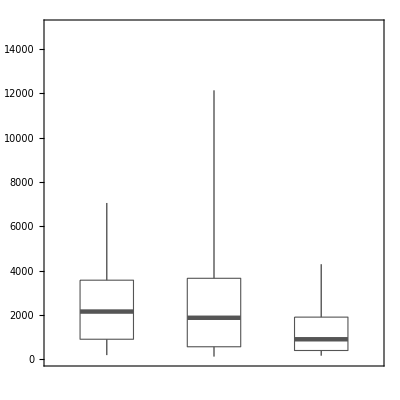

```mathematica
bwchart = BoxWhiskerChart[a0,{ {"MedianMarker",Directive[Thickness[.008],Darker[Gray]]},{"Whiskers",Directive[Thick,Darker[Gray]]},{"Fences",1,Opacity[0]}} ,PlotRange-> {0,15000},  ChartStyle->{{EdgeForm[{Darker[Gray], Thickness[Large]}  ]} , {White} } , AspectRatio->1 ,{Method->{"BoxRange"->(Quantile[#,{.05,.25,.5,.75,.95},{{1,-1},{0,1}}]&)}}]
```

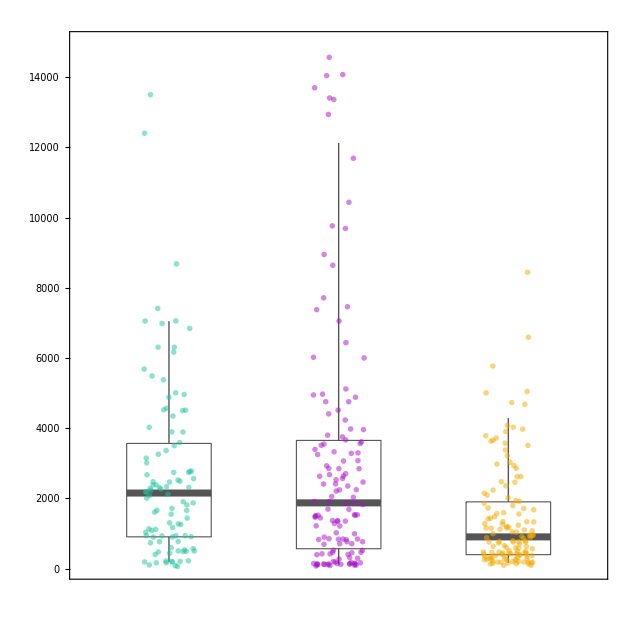

```mathematica
Show[   bwchart,b, AspectRatio -> 1,myfont]
```

#### MannWhitney Tests...

```mathematica
MannWhitneyTest[ {a[[1]],a[[4]]} ]  (*TA?*)
MannWhitneyTest[ {a[[2]],a[[4]]} ]  (*TA?*)
MannWhitneyTest[ {a[[3]],a[[4]]} ]  (*TA?*)
MannWhitneyTest[ {a[[2]],a[[3]]} ]
MannWhitneyTest[ {a[[1]],a[[3]]} ]
MannWhitneyTest[ {a[[1]],a[[2]]} ]
```

0.0000104071

0.0000366542

0.000389312

0.63556

0.65313

0.945704

#### Next...